```mathematica
DeltaxCC[β_,u_,v_,p_,b_,c_,n_]:=β(1-p/2)*(-(b-c)-c*n)*1/4((n-1)/n)(1-1/2((n*u+2(1-p/2))/(n*u+(1-p/2))))
```

{β→0.001,u→0.001,v→0.005,b→1.,c→0.2,n→40}

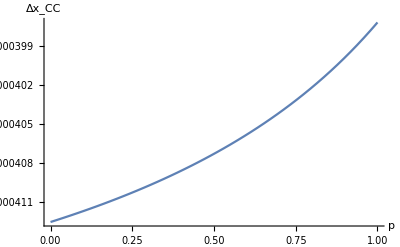

```mathematica
params = {β->0.001, u->0.001,v->0.005,b->1.0,c->0.2,n->40}
Plot[DeltaxCC[β,u,v,p,b,c,n]/.params,{p,0,1}, AxesLabel->{p,Subscript[Δx, CC]}]
```

## Testing y values / fitting with n = 20

```mathematica
params = {u->0.001,n->20};data={{0.00,0.9906158505270576},{0.25,0.9900787436852271},{0.5,0.9906706047376032},{0.75,0.9900556300009499},{0.99,0.9671585705214603},{0.995,0.9568391557812266}, {0.999,0.8582948968078467}}; (*,{1.0,0.7566712846775426}};*)
model=(2+n u)/(2+2 n u)(1-p)^a/.params;
fit=FindFit[data,model,{a},p]
```

{a→0.0124612}

0.990196 (1-p)^0.0124612

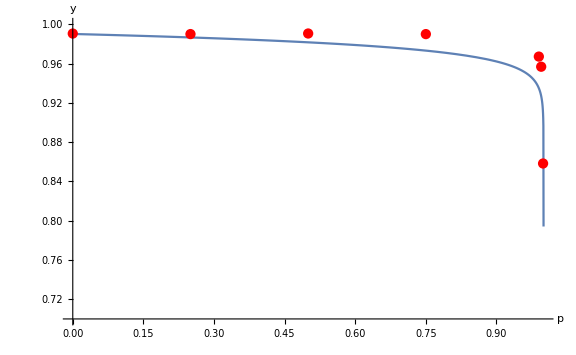

```mathematica
model/.fit/.params
p1=Plot[model/.fit/.params,{p,0,1}, AxesLabel->{p,y},PlotRange->{Automatic,{0.7,1}}];
p2=ListPlot[data,PlotStyle->Red];
Show[p1,p2,ImageSize->Large]
```

#### OLD: Check y and integrate

```mathematica
(*OLD: Check the manual derivation of y(τ)*)
tt[τ_,n_,p_]:=τ*(n^2/(2(1-p/2)))
yt[t_,n_,p_,u_]:=1/2(1+(1-u/n(1-p/2))^(2*t))
yt[tt[τ,n,p],n,p,μ/n];
(*take the limit after replacing t=τ*(n^2/(2(1-p/2))) and u=μ/n*)
ytau[μ_,τ_,p_]:=Limit[y[tt[τ,n,p],n,p,μ/n],n->Infinity]
ytau[μ,τ,p]
```

1/2 (1+ⅇ^(-μ τ))

```mathematica
(*OLD: Check the integration of y*)
ρ[μ_,τ_,p_]:=Exp[-τ]
y[μ_,p_]:=Integrate[ytau[μ,τ,p]*ρ[μ,τ,p], {τ,0,Infinity}][[1]]
y[μ,p]/.{μ->n*u}
```

(2+n u)/(2+2 n u)

```mathematica
(*OLD: Check what happens if we change to τ=t/(n^2/2),μ=n(1-p/2)*)
tt[τ_,n_,p_]:=τ*(n^2/2)
yt[t_,n_,p_,u_]:=1/2(1+(1-u/n(1-p/2))^(2*t))
yt[tt[τ,n,p],n,p,μ/(n(1-p/2))];
(*take the limit after replacing t=τ*(n^2/2) and u=μ/(n(1-p/2)))*)
ytau[μ_,τ_,p_]:=Limit[y[tt[τ,n,p],n,p,μ/(n(1-p/2))],n->Infinity]
ytau[μ,τ,p]
```

1/2 (1+ⅇ^(-μ τ))

```mathematica
(*OLD: Check integration with τ=t/(n^2/2)*)
ρ[μ_,τ_,p_]:=(1-p/2)*Exp[-(1-p/2)τ]
y[μ_,p_]:=Integrate[ytau[μ,τ,p]*ρ[μ,τ,p], {τ,0,Infinity}][[1]]
y[μ,p]/.{μ->n*u(1-p/2)} // FullSimplify
(*should get the same result as with the other rescaling*)
```

(2+n u)/(2+2 n u)

```mathematica
(*checking the error*)
Plot[{1-p/2,1-(n*p)/(2(n-1))/.params},{p,0,1},PlotLabels->Automatic,PlotRange->{0,1},ImageSize->Large]
```

-Graphics-

## Computing y

```mathematica
γ[n_,p_]:=1-(n*p)/(2(n-1))
tt[τ_,n_,p_]:=τ*(n^2/(2γ[n,p]))
ρ[τ_,p_]:=Exp[-τ]
ρ2[τ3_,τ2_]:=3*Exp[-3*τ3]Exp[-τ2]
```

```mathematica
(*Check the manual derivation of y(τ)*)
yt[t_,n_,p_,u_]:=1/2(1+(1-u/n γ[n,p])^(2*t))
yt[tt[τ,n,p],n,p,μ/n];
(*take the limit after replacing t=τ*(n^2/(2(1-p/2))) and u=μ/n*)
ytau[μ_,τ_,p_]:=Limit[yt[tt[τ,n,p],n,p,μ/n],n->Infinity]
ytau[μ,τ,p]
```

1/2 (1+ⅇ^(-μ τ))

```mathematica
(*Check the integration of y*)
y[μ_,p_]:=Integrate[ytau[μ,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
(*prep a function for computing the values more quickly*)
ycalc[n_,u_,v_]=y[μ,p]/.{μ->n*u};
```

```mathematica
ycalc[n,u,v]
```

(2+n u)/(2+2 n u)

## Computing z

```mathematica
(*Check what happens if we change to τ=t/(n^2/2γ), μ=νu *)
zt[t_,n_,p_,v_]:=(1-v/n γ[n,p])^(2*t)
(*take the limit after replacing t=τ*(n^2/(2γ)) and v=ν/n)*)
ztau[ν_,τ_,p_]:=Limit[zt[tt[τ,n,p],n,p,ν/n],n->Infinity]
ztau[ν,τ,p]
```

ⅇ^(-ν τ)

```mathematica
(*Check integration with τ=t/(n^2/2γ)*)
z[ν_,p_]:=Integrate[ztau[ν,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
(*prep a function for computing the values more quickly*)
zcalc[n_,u_,v_]=z[ν,p]/.{ν->n*v} // FullSimplify;
```

```mathematica
zcalc[n,u,v]
```

1/(1+n v)

## Computing g

```mathematica
(*Check what happens if we change to τ=t/(n^2/2γ), μ=nu *)
gtau[μ_,ν_,τ_,p_]:=ytau[μ,τ,p]*ztau[ν,τ,p]
gtau[μ,ν,τ,p]
```

1/2 ⅇ^(-ν τ) (1+ⅇ^(-μ τ))

```mathematica
(*Check integration with τ=t/(n^2/2γ)*)
g[μ_,ν_,p_]:=Integrate[gtau[μ,ν,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
(*prep a function for computing the values more quickly*)
gcalc[n_,u_,v_]=g[μ,ν,p]/.{ν->n*v,μ->n*u}// FullSimplify;
```

```mathematica
gcalc[n,u,v](*check*)
```

1/2 (1/(1+n v)+1/(1+n (u+v)))

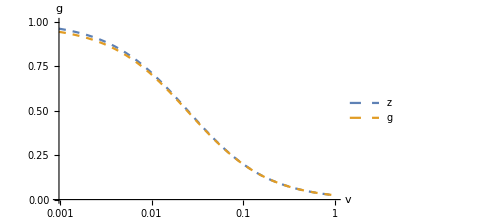

```mathematica
params={β->0.001,u->0.001,n->40};
LogLinearPlot[{zcalc[n,u,v]/.params,gcalc[n,u,v]/.params},{v,0,1},PlotRange->{0,1},AxesLabel->{"v","g"},PlotLegends->Placed[{"z","g"},{0.9,0.5}],ImageSize->Medium,PlotStyle->Dashed]
(*these functions are different but the difference is smalll when u is small*)
```

## Computing h

```mathematica
htau[μ_,ν_,τ3_,τ2_,p_]:=1/3(ytau[μ,τ3,p]*ztau[ν,τ3+τ2,p]+ytau[μ,τ3+τ2,p]*ztau[ν,τ2,p]+ytau[μ,τ3+τ2,p]*ztau[ν,τ3+τ2,p])
h[μ_,ν_,p_]:=Integrate[htau[μ,ν,τ3,τ2,p]*ρ2[τ3,τ2], {τ2,0,Infinity},{τ3,0,Infinity}][[1]]
(*prep a function for computing the values more quickly*)
hcalc[n_,u_,v_]=h[μ,ν,p]/.{ν->n*v,μ->n*u} // FullSimplify// Apart;
```

```mathematica
hcalc[n,u,v]
```

(11+4 n u)/(6 (2+n u) (1+n v))-1/(2 (3+n v))+(5+n u)/(4 (3+n u) (1+n u+n v))+(-4-n u)/(4 (2+n u) (3+n u+n v))

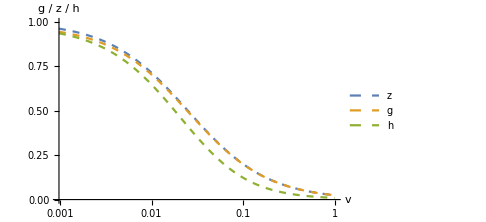

```mathematica
(*plot all three quantities: g, y, *)
params={β->0.001,u->0.001,n->40};
expressions={ zcalc[n,u,v](*z*) ,gcalc[n,u,v](*g*), hcalc[n,u,v](*h*)}/.params;
LogLinearPlot[expressions,{v,0,1},PlotRange->{0,1},AxesLabel->{"v","g / z / h"},PlotLegends->Placed[{z,g,h},{0.9,0.5}],ImageSize->Medium,PlotStyle->Dashed]
```

## Compute theoretical predictions and export data

```mathematica
Clear[n,β,p,u,v,params];
params={n->40,u->0.001,β->0.001};

(*generate a list of vs finer than the sims*)
vs=Table[10^log10v,{log10v,-3,Log10[0.625],(Log10[0.005] - Log10[0.001])/2/2}];
(*ps =Table[p,{p,0,1,0.25}];*) (*we know that y, z, g, h is independent of p*)
(*compute y,z,g,h for each (u,v) pair*)
data=Flatten[
Table[{u/.params,v,ycalc[n,u,v]/.params,
zcalc[n,u,v]/.params,gcalc[n,u,v]/.params,hcalc[n,u,v]/.params},
{v,vs}],
0]; (*flatten into a data table*)
headers={"u","v","y","z","g","h"};
data=Prepend[data,headers];

filename="~/.julia/dev/CooperationPolarization2/data/calc_data/calc_data.csv";
Export[filename,data]
```

~/.julia/dev/CooperationPolarization2/data/calc_data/calc_data.csv

```mathematica
data//MatrixForm (*exported data*)
```

(u | v | y | z | g | h
0.001 | 0.001 | 0.980769 | 0.961538 | 0.943732 | 0.935249
0.001 | 0.00149535 | 0.980769 | 0.943562 | 0.926403 | 0.914037
0.001 | 0.00223607 | 0.980769 | 0.9179 | 0.901646 | 0.883833
0.001 | 0.0033437 | 0.980769 | 0.88203 | 0.867001 | 0.841773
0.001 | 0.005 | 0.980769 | 0.833333 | 0.819892 | 0.784999
0.001 | 0.00747674 | 0.980769 | 0.769782 | 0.758284 | 0.711551
0.001 | 0.0111803 | 0.980769 | 0.690983 | 0.681691 | 0.621685
0.001 | 0.0167185 | 0.980769 | 0.599254 | 0.59224 | 0.519158
0.001 | 0.025 | 0.980769 | 0.5 | 0.495098 | 0.411507
0.001 | 0.0373837 | 0.980769 | 0.400746 | 0.397584 | 0.308473
0.001 | 0.0559017 | 0.980769 | 0.309017 | 0.30713 | 0.218936
0.001 | 0.0835925 | 0.980769 | 0.230218 | 0.229168 | 0.148079
0.001 | 0.125 | 0.980769 | 0.166667 | 0.166115 | 0.0965029
0.001 | 0.186919 | 0.980769 | 0.11797 | 0.117693 | 0.0614246
0.001 | 0.279508 | 0.980769 | 0.0820995 | 0.0819651 | 0.0386959
0.001 | 0.417963 | 0.980769 | 0.0564382 | 0.0563746 | 0.0243834
0.001 | 0.625 | 0.980769 | 0.0384615 | 0.038432 | 0.0154707)